```mathematica
Nearest[WordList[],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

```mathematica
Table[Blur[-Graphics-, r], {r, 0, 22, 2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ImageIdentify[Blur[-Graphics-, r]], {r, 0, 22, 2}]
```

{cheetah,cheetah,cheetah,cheetah,wildcat,Canada lynx,feline,nutria,musteline mammal,northern river otter,whortleberry,whortleberry}

```mathematica
ImageIdentify[-Graphics-,All,10,"Probability"]
```

<|wildcat→0.316966,liger→0.264208,lynx→0.194644,Canada lynx→0.189105,jaguar→0.182134,mountain lion→0.120258,cheetah→0.114714,patas monkey→0.0424091,baboon→0.0261085,chacma baboon→0.0259168|>

```mathematica
FindClusters[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

{{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},{RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}]},{RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}]}}

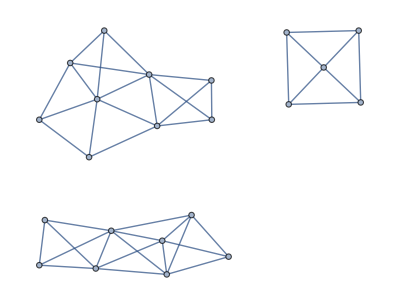

```mathematica
NearestNeighborGraph[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},3,VertexLabels->All]
```

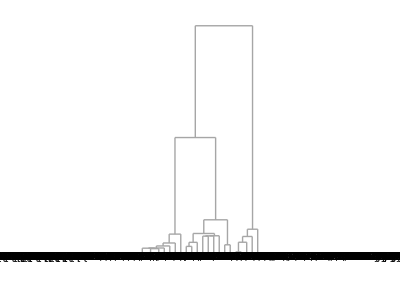

```mathematica
Dendrogram[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

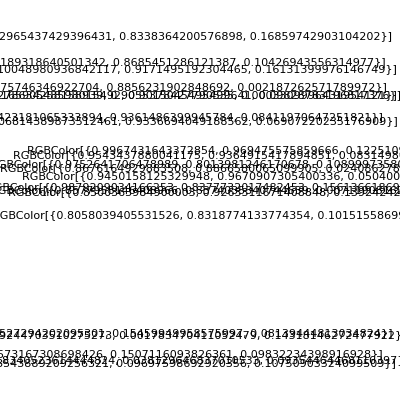

```mathematica
FeatureSpacePlot[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

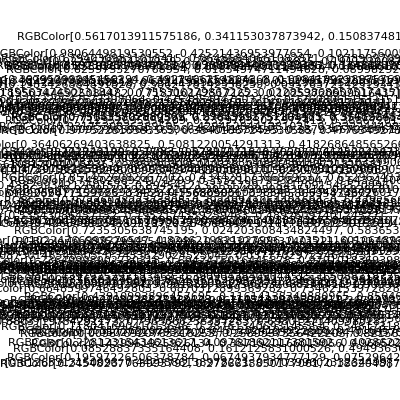

```mathematica
FeatureSpacePlot[RandomColor[200]]
```

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[Table[Rasterize[FromLetterNumber[n]],{n,26}]]
```

-Graphics-

```mathematica
FeatureSpacePlot[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

-Graphics-

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

100

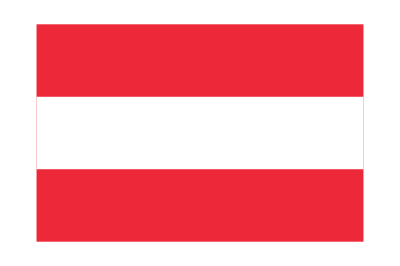
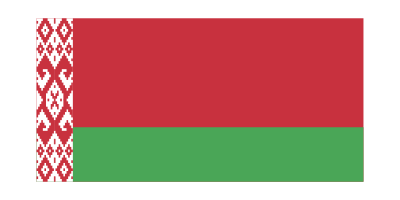
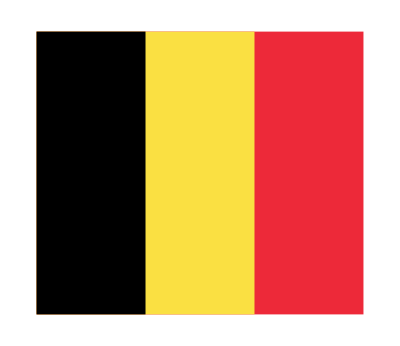
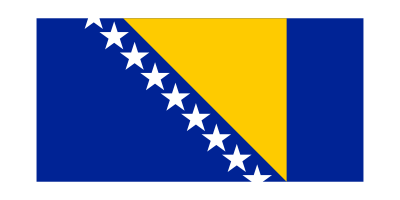
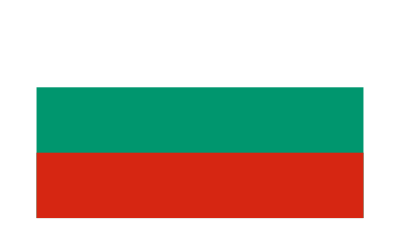
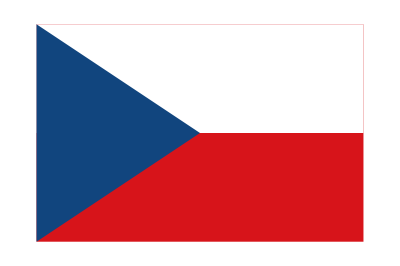
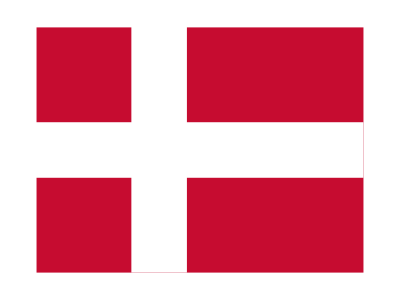
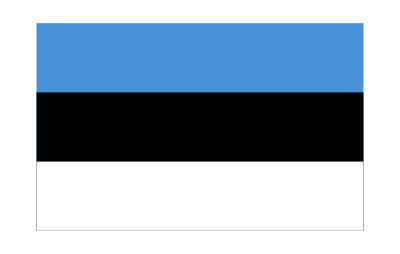


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[a["Flag"],{a,Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]]}]
```

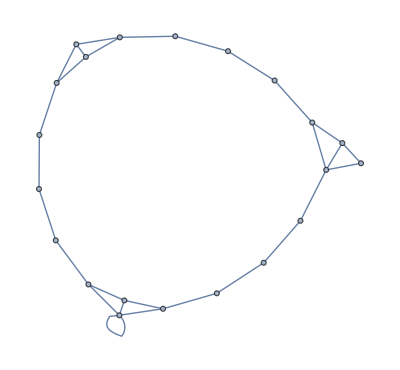

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,.05}],2,VertexLabels->All]
```

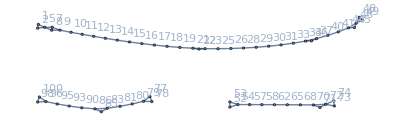

```mathematica
NearestNeighborGraph[RandomInteger[100,100],2,VertexLabels->All]
```

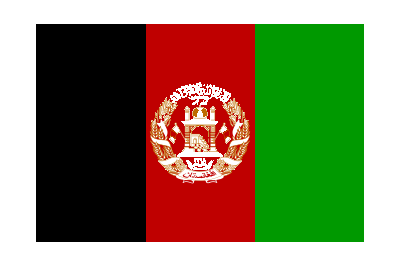
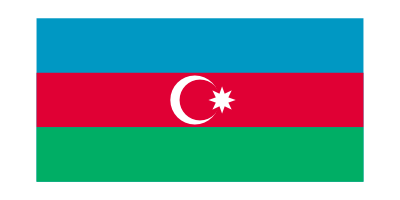
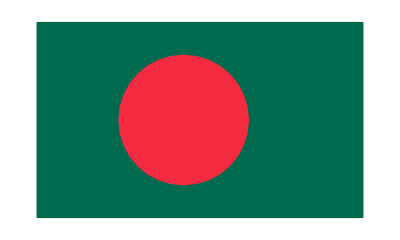
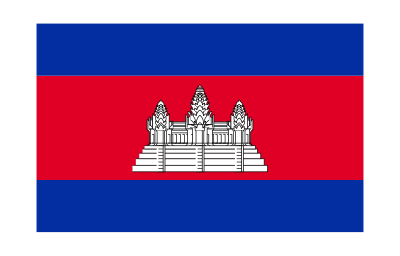
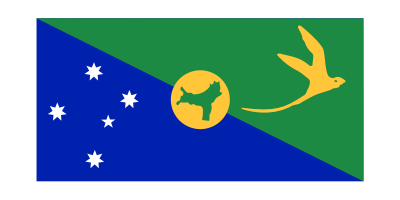
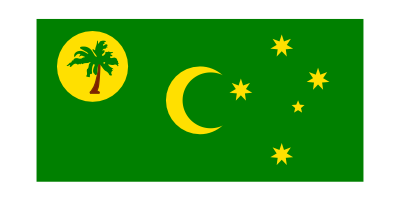
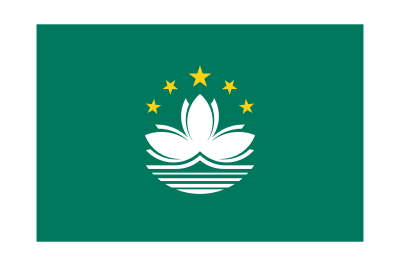
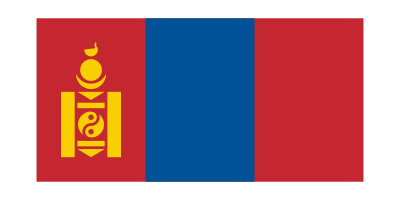

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[Table[a["Flag"],{a,Entity["GeographicRegion","Asia"][EntityProperty["GeographicRegion","Countries"]]}]]
```

```mathematica
Nearest[Flatten[Table[i/j,{i,500},{j,500}]],π,10]
```

{355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155}

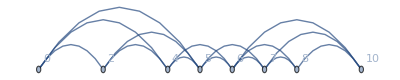

```mathematica
NearestNeighborGraph[RandomInteger[10,10],3,VertexLabels->All]
```

```mathematica
FindClusters[RandomColor[100]]
```

{{RGBColor[0.027903991662851402, 0.8285383729599483, 0.19279912535904775],RGBColor[0.5586506128181092, 0.8442719457296504, 0.1707033234476809],RGBColor[0.32960706875613677, 0.9549120591668352, 0.176647508275928],RGBColor[0.49230876111770216, 0.9846786022239238, 0.0056361311498152045],RGBColor[0.2219406824947845, 0.742996917737943, 0.14782399621925513],RGBColor[0.45354163835318806, 0.7237816038462854, 0.5154347883272998],RGBColor[0.6116784551679924, 0.6855749541515648, 0.0983907491404612],RGBColor[0.36572107750356864, 0.7984127913310526, 0.22123333100515685],RGBColor[0.594753986505737, 0.8388395843096235, 0.012760360530774228],RGBColor[0.023236824663172007, 0.829785414782523, 0.4562225341669226],RGBColor[0.5053382749712989, 0.6239716486985438, 0.16244974480516605],RGBColor[0.06390598196124775, 0.7011869593181705, 0.21288960588955996],RGBColor[0.5424131855242891, 0.9605010813381285, 0.11557538631089637],RGBColor[0.06517782958845841, 0.7943969910882085, 0.29656804907808465],RGBColor[0.22029628731225115, 0.6413413708178075, 0.4305074081767202],RGBColor[0.0190169529526103, 0.6038311117313087, 0.25393757092777247],RGBColor[0.5996739952187404, 0.5856863919197624, 0.2148905929947773],RGBColor[0.05451785030894607, 0.7532515198980962, 0.08550268558126839],RGBColor[0.5556827905082062, 0.9503402890834372, 0.3916207527061206],RGBColor[0.523382926991173, 0.8149996280457148, 0.21866651318232777],RGBColor[0.4395188580075262, 0.6562603243755398, 0.099183884185571],RGBColor[0.5058712270687855, 0.7248323850502536, 0.11436593526013072],RGBColor[0.2796632094856415, 0.717340079334863, 0.3419737769314457],RGBColor[0.5803121060096423, 0.8656875801687376, 0.19066704633884557],RGBColor[0.8645614857731097, 0.8866097094650607, 0.5452148088477411]},{RGBColor[0.5977523885739862, 0.6039667373793847, 0.4032523963997645],RGBColor[0.6511921339626008, 0.6555738376847398, 0.5340228135333467]},{RGBColor[0.5451836259851024, 0.49443122419672547, 0.5909978445597353],RGBColor[0.364800692277925, 0.5830211485745556, 0.6175832417574463],RGBColor[0.01859697596228571, 0.5103047932040106, 0.513827859637662],RGBColor[0.4927453482813431, 0.6339033669686143, 0.8343371199596445],RGBColor[0.5770648810789358, 0.7686435151130175, 0.7968128057567516],RGBColor[0.5018488242200516, 0.6021855673618384, 0.6927410714471678],RGBColor[0.5516123279605081, 0.621371424880097, 0.6881082297894305],RGBColor[0.21095210562288602, 0.3079943114205064, 0.415501304464055]},{RGBColor[0.0012269748182205387, 0.523207092304222, 0.8668266496616837],RGBColor[0.0002618947972718999, 0.18423703765470822, 0.9855076757382297],RGBColor[0.15725093576234972, 0.12469308655780242, 0.7113992373795313],RGBColor[0.19688085132363753, 0.3714835234448113, 0.9163525891202384],RGBColor[0.5300951900620818, 0.0847073078950622, 0.8692166149473952],RGBColor[0.5881227548072923, 0.41780709800556015, 0.7168753185411492],RGBColor[0.029652955856106278, 0.31528971777015635, 0.8258433281068465],RGBColor[0.5277787384130468, 0.22539612931958186, 0.9453698575727099],RGBColor[0.3531175101895925, 0.3387981772736044, 0.7764558324655608],RGBColor[0.3758510711868355, 0.25030731036447373, 0.6760557326302465],RGBColor[0.05021213205674813, 0.15796395599874646, 0.6989170279937982],RGBColor[0.6156455221681856, 0.4772551407403829, 0.9404519401809321],RGBColor[0.5603279800478693, 0.5990816279574627, 0.9730005860852915],RGBColor[0.4404080862269344, 0.3658990163437752, 0.8557490994002601],RGBColor[0.30867081547638775, 0.3109595344742162, 0.6444936235532297],RGBColor[0.14515108114218078, 0.1706606304896059, 0.7889249704507082],RGBColor[0.19102670197931526, 0.22881752176287762, 0.7468077900730838],RGBColor[0.6675490388451792, 0.5802202166504156, 0.8765237023726846],RGBColor[0.18199186309323112, 0.16758838838180634, 0.7004626223600727]},{RGBColor[0.10670474303721966, 0.13858083776158936, 0.04259097703161552],RGBColor[0.028937162900847913, 0.4195778756504014, 0.2698106750137219],RGBColor[0.1111672324414883, 0.31076556747991857, 0.13164896449065],RGBColor[0.331905598480831, 0.48008766690416205, 0.18723927794000095]},{RGBColor[0.4913342928978004, 0.06636761688800141, 0.6681245892834522],RGBColor[0.6544347363171312, 0.2367333187853602, 0.7852424004895129],RGBColor[0.9310127260381185, 0.25615122204075247, 0.9033041995450646],RGBColor[0.7761565986395604, 0.3388726365920878, 0.9640326639390504],RGBColor[0.5039303022383721, 0.08083793811297535, 0.7284268078538538],RGBColor[0.9131755527140633, 0.3292676079871415, 0.9107093807601985],RGBColor[0.5267980870644129, 0.02679663378011221, 0.6754497280901932],RGBColor[0.9430403497333368, 0.05062180867967658, 0.8230031100264421]},{RGBColor[0.128920724067084, 0.7618445062041188, 0.7792817659702538],RGBColor[0.311046430031112, 0.9295669865452634, 0.7951242437250798],RGBColor[0.06164851272686356, 0.8963492466717904, 0.590684802646859],RGBColor[0.1306483872539077, 0.925056868668451, 0.8544581433744063],RGBColor[0.3959160880627357, 0.8943950920688555, 0.8053603264054494],RGBColor[0.23309232252368295, 0.9405992040066427, 0.6215291302354666]},{RGBColor[0.816139440975638, 0.25236502471356803, 0.49010049458606786],RGBColor[0.8260909621814114, 0.18665852861980015, 0.59672149806218],RGBColor[0.9415895603759534, 0.11247150272426598, 0.20740159683202442],RGBColor[0.7047297748550008, 0.24529387579904882, 0.2242578698524449],RGBColor[0.7092995154039456, 0.4338543717188619, 0.5914852865010078],RGBColor[0.6523137722166397, 0.1438739175761099, 0.14669511861246032],RGBColor[0.7179784862956469, 0.35350743386691397, 0.4071152188233571],RGBColor[0.7841335231977089, 0.0784626991541868, 0.26243408701580573],RGBColor[0.6910240068862101, 0.09462528799049585, 0.36478129908517776]},{RGBColor[0.8376256537198306, 0.5520266199034509, 0.3474470760533883],RGBColor[0.6694439871915854, 0.45143401058215704, 0.1296468337426322],RGBColor[0.7095808661629255, 0.23793845437623085, 0.18134259372366346],RGBColor[0.7491491185894334, 0.12390016143999971, 0.05555468859884183],RGBColor[0.9448063682165619, 0.3619233058503355, 0.269413540182478]},{RGBColor[0.8514367134893448, 0.9082539579142948, 0.3428825821093817],RGBColor[0.926947175125195, 0.7886728659592515, 0.13831825030904588],RGBColor[0.9817229411470898, 0.7747520438704425, 0.16062120225000975],RGBColor[0.9604976976094144, 0.8365495225716502, 0.06096530833529323]},{RGBColor[0.3750932186496627, 0.24519311488713624, 0.24337786168083597],RGBColor[0.44138172569923495, 0.11973015248255425, 0.17218155450792727],RGBColor[0.6052918511196517, 0.2344052298649577, 0.21754288733889982],RGBColor[0.7696269695152598, 0.5175511841300506, 0.5712569482639756],RGBColor[0.4464763129383864, 0.15123789831369416, 0.19283520029120704],RGBColor[0.4134067374987187, 0.24228355577456973, 0.195820201999517]},{RGBColor[0.42890940442174363, 0.10743436312632926, 0.29703528536900947],RGBColor[0.2623146185067502, 0.012207350647876147, 0.16810216953341794],RGBColor[0.2663725786108395, 0.010601842789162319, 0.3409559971661287],RGBColor[0.13494584068521398, 0.27113489442717786, 0.5330527646813943]}}

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
FeatureSpacePlot[Table[Rasterize[a],{a,Join[ToUpperCase[Alphabet[]],Alphabet[]]}]]
```

-Graphics-

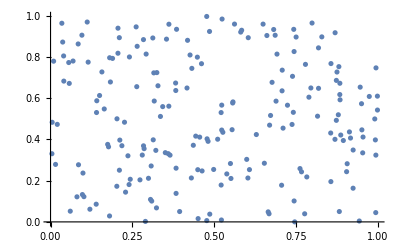

```mathematica
ListPlot[Table[{RandomReal[],RandomReal[]},200]]
```

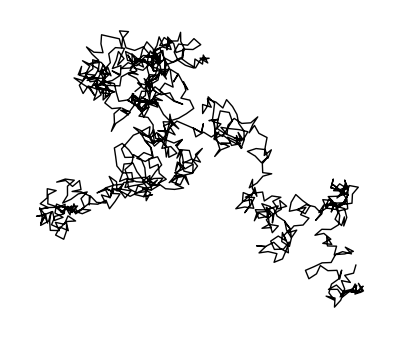

```mathematica
Graphics@Line[AnglePath[Table[RandomReal[2π],1000]]]
```

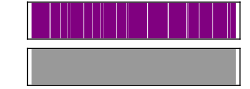

```mathematica
Sound@Table[SoundNote["C",RandomReal[0.5]],20]
```

```mathematica
ArrayPlot[Table[Mod[i,j],{i,50},{j,50}]]
```

-Graphics-

```mathematica
Table[ArrayPlot[Table[Mod[x^y,n],{x,50},{y,50}]],{n,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Round[π-3,10^-50]
```

14159265358979323846264338327950288419716939937511/100000000000000000000000000000000000000000000000000

```mathematica
N[Power[0.1,50]]
```

1.×10^-50

```mathematica
Total[Table[Prime[n],{n,1,1000}]]
```

3682913

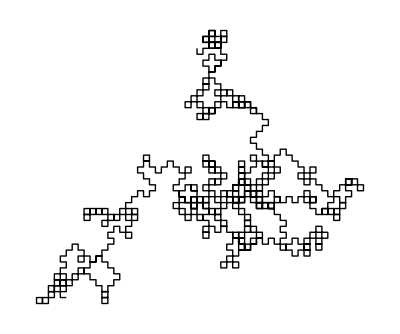

CountsBy[{hello,he,hello}]

```mathematica
Graphics[Line[AnglePath[Table[Mod[Prime[n],4]*90°,{n,1000}]]]]
```

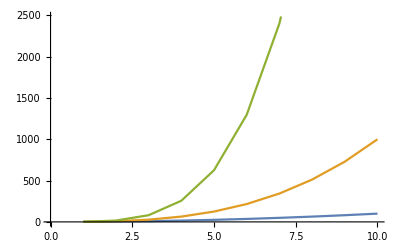

```mathematica
ListLinePlot[Table[i^j,{j,2,4},{i,10}]]
```

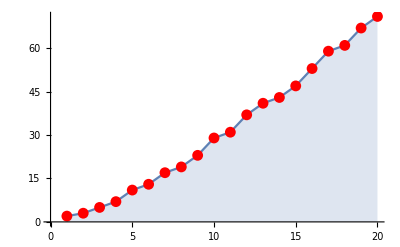

```mathematica
ListLinePlot[Table[Prime[n],{n,1,20}],Mesh->All,MeshStyle->Red,Filling->Axis]
```

```mathematica
ListPlot3D[Table[{i,j,Mod[i,j]},{i,100},{j,100}],Mesh->All]
```

-Graphics3D-

```mathematica
Flatten[Table[{i,j,Mod[i,j]},{i,10},{j,10}],1]
```

{{1,1,0},{1,2,1},{1,3,1},{1,4,1},{1,5,1},{1,6,1},{1,7,1},{1,8,1},{1,9,1},{1,10,1},{2,1,0},{2,2,0},{2,3,2},{2,4,2},{2,5,2},{2,6,2},{2,7,2},{2,8,2},{2,9,2},{2,10,2},{3,1,0},{3,2,1},{3,3,0},{3,4,3},{3,5,3},{3,6,3},{3,7,3},{3,8,3},{3,9,3},{3,10,3},{4,1,0},{4,2,0},{4,3,1},{4,4,0},{4,5,4},{4,6,4},{4,7,4},{4,8,4},{4,9,4},{4,10,4},{5,1,0},{5,2,1},{5,3,2},{5,4,1},{5,5,0},{5,6,5},{5,7,5},{5,8,5},{5,9,5},{5,10,5},{6,1,0},{6,2,0},{6,3,0},{6,4,2},{6,5,1},{6,6,0},{6,7,6},{6,8,6},{6,9,6},{6,10,6},{7,1,0},{7,2,1},{7,3,1},{7,4,3},{7,5,2},{7,6,1},{7,7,0},{7,8,7},{7,9,7},{7,10,7},{8,1,0},{8,2,0},{8,3,2},{8,4,0},{8,5,3},{8,6,2},{8,7,1},{8,8,0},{8,9,8},{8,10,8},{9,1,0},{9,2,1},{9,3,0},{9,4,1},{9,5,4},{9,6,3},{9,7,2},{9,8,1},{9,9,0},{9,10,9},{10,1,0},{10,2,0},{10,3,1},{10,4,2},{10,5,0},{10,6,4},{10,7,3},{10,8,2},{10,9,1},{10,10,0}}

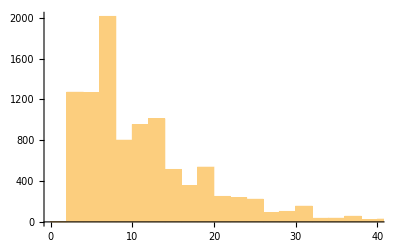

```mathematica
Histogram[Table[Prime[n+1]-Prime[n],{n,1,10000}]]
```

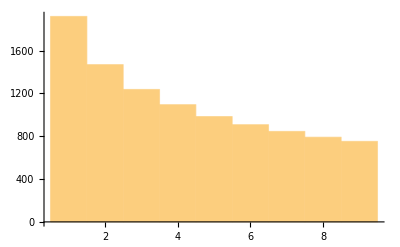

```mathematica
Histogram[Table[IntegerDigits[n^2][[1]],{n,10000}]]
```

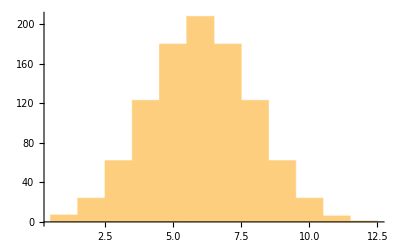

```mathematica
Histogram[Table[RomanNumeral[n],{n,1000}]//StringLength]
```

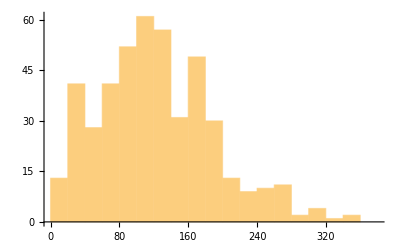

```mathematica
Histogram[StringLength@TextSentences[WikipediaData["computers"]]]
```

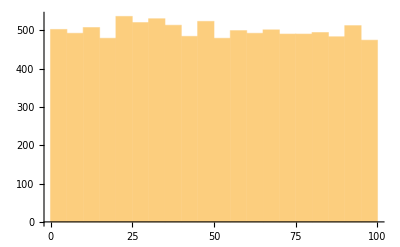
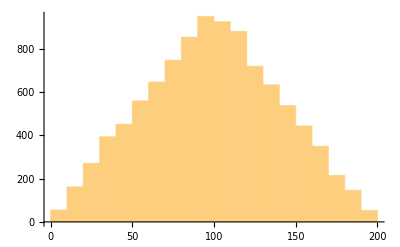
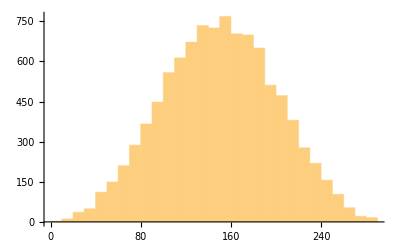
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[Table[Total[Table[RandomReal[100],n]],10000]],{n,5}]
```

```mathematica
ImageData[Binarize[Rasterize[Style["W",200]]]]
```

{234,110}

```mathematica
ListPlot3D@ImageData[ColorNegate[Binarize[Rasterize[Style["W",200]]]]]
```

-Graphics3D-

```mathematica
ListPlot3D@ImageData[Total[ColorSeparate[-Graphics-]]/3]
```

-Graphics3D-

```mathematica
ColorSeparate[-Graphics-]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Max[ColorSeparate[-Graphics-]]
```

1.

```mathematica
Total[ColorSeparate[-Graphics-]]/3
```

-Graphics-

```mathematica
Grid[ImageData[-Graphics-]]
```

1
 |  |  |  |

```mathematica
ListPlot3D@ImageData[ColorNegate@Binarize[-Graphics-]]
```

-Graphics3D-

```mathematica
list= {0,0,0,0,0,1,1,1,1,1,0,0,0,0,0};
res=LaplacianFilter[list,1]//Chop
```

{0,0,0,0,2.85991,-2.85991,0,0,0,-2.85991,2.85991,0,0,0,0}

```mathematica
Table[LaplacianFilter[-Graphics-,r],{r,1,1000,500}]
```

{-Graphics-,-Graphics-}

```mathematica
(mat=N@BoxMatrix[1,7])//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 1. | 1. | 0. | 0.
0. | 0. | 1. | 1. | 1. | 0. | 0.
0. | 0. | 1. | 1. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
LaplacianFilter[mat,1]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.157807 | 1.68439 | 1.52658 | 1.68439 | -0.157807 | 0.
0. | 1.68439 | -3.21096 | -1.52658 | -3.21096 | 1.68439 | 0.
0. | 1.52658 | -1.52658 | 0. | -1.52658 | 1.52658 | 0.
0. | 1.68439 | -3.21096 | -1.52658 | -3.21096 | 1.68439 | 0.
0. | -0.157807 | 1.68439 | 1.52658 | 1.68439 | -0.157807 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
ImageAdjust[DistanceTransform[-Graphics-]]
```

-Graphics-